## Setup

```mathematica
Get["FunKit`"]
```

Mathematica package TensorBases loaded
Authors: Andreas Geißel, Franz Richard Sattler
Version: 1.0
Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.
For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

Other useful tools include TBBasisTransformation, TBVertexTransformation, TBGetIdentityMatrix, TBGetBasisSize, TBGetIndexSet, TBMakePropagator.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package loaded.

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].
Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

Lorentz group undefined, using default names.

Group with name color undefined, using default names.

Group with name flavor undefined, using default names.

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.2.3
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

Please note for this file, that detailed explanations of any function can be found with Function::usage, e.g.

```mathematica
FTakeDerivatives::usage
```

FTakeDerivatives[setup, expr, derivativeList]
Takes multiple functional derivatives of expr with respect to the fields specified in derivativeList.
Returns the result with all derivative operators resolved.
FTakeDerivatives[setup, expr, derivativeList, "Symmetries" -> symmetries] allows specifying symmetries for simplification.
The derivativeList should be a list of field expressions like {A[i1], A[i2]}.

Also, you can use FInfo[] in any Notebook to get an explanation of some general concepts of FunKit

In the following, we define the gauge-fixed Yang-Mills theory and the truncation used.
First, we define our field space that includes bosonic and fermionic fields A (gluons) and cb,c (ghosts)

```mathematica
fields=<|
"Commuting"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
```

Next, the truncation specifies which interactions are taken into account, for each kind of object that can appear in an equation. To see all objects, call ShowIndexedObjects[]. In the following, we set the truncation for fields explicitly to nothing, as we wish to look at the symmetric (vacuum) phase of Yang-Mills theory.

```mathematica
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
```

The bases used for explicit tracing of the expressions are specified next. This is used by FunKit to create diagrammatic rules with FMakeDiagrammaticRules[Setup] later on; of course, you can also specify the diagrammatic rules by hand.
If you want to use FMakeDiagrammaticRules, any basis must be known to TensorBases, the framework used by FunKit to manage vertex bases. To see how to define new bases, see both the corresponding publication https://arxiv.org/abs/2503.05580 and the TensorBases showcase notebook at https://github.com/satfra/TensorBases/blob/main/examples/Showcase.nb
To see a list of all available bases, call TBInfo[] and for information on a specific basis TBInfo[“AA”], here at the example of the two-gluon basis.

In the bases Association, we now attach a list of vertex rules to each object that should be written out using TensorBases. There are several ways to specify a basis:
  1. GammaN->{{A, A, A} -> “AAAClass”, ...} simply leads to FunKit using the full basis “AAAClass” for any object GammaN[{A,A,A},{....}]
  2. GammaN->{{A, qb, q} -> {“AqbqDirect”, 1,4,7}, ...} leads to FunKit using the elements 1, 4 and 7 from the basis “AqbqDirect” for any object GammaN[{A,qb,q},{....}]
  3. GammaN->{{A, sb,s} -> {“AqbqDirectSF”, 1,4,7,s->q,sb->qb}, ...} leads to FunKit using the elements 1, 4 and 7 from the basis “AqbqDirectSF” for any object GammaN[{A,sb,s},{....}]
For the third example, the  additional rules are needed to translate the names of fields as used in the basis to the one used in your code.

```mathematica
bases=<|
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
```

DiagramStyling does exactly what it sounds like: You can give line-styles for propagators with the associated fields in Feynman diagrams. Note that for paired fields (fermion/antifermion, or complex scalars) you only need to specify one of both.

```mathematica
diagramStyling=<|
"Styles"->{A->{Orange},c->{Black,Dashed}}
|>;
```

Finally, the setup Association puts the specifics of the theory defined above together and is passed to FunKit as the Global Setup to be used in all calls to FunKit’s functions.
Note that it is not necessary to set a global setup, instead one could also pass Setup as the first parameter to all functions - as this is usually more cumbersome, however, we opt for setting the setup globally.

```mathematica
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;
FSetGlobalSetup[Setup];
```

Finally, to get correctly formatted LaTeX output, we can add some custom replacements for the FTex and FPrint commands, which we use to actually put a bar above the anti - ghost field instead of printing out cb.

```mathematica
FSetTexStyles[cb->"\\bar{c}"];
```

Using the MakeDiagrammaticRules command, FunKit will produce output where every vertex is dressed with a dressing[Object, {fields, ...}, basisIndex, {momenta, ...}]. We want to explicitly parameterise these dressings with wavefunctions, so we define the function dressingRules in the following:

```mathematica
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},2,{a_,b_}]:>ξ^-1,
dressing[GammaN,{cb,c},1,{p1_,p2_}]:>-Zc[√sp[p2,p2]]sp[p2,p2],

dressing[InverseProp,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[InverseProp,{A,A},2,{a_,b_}]:>ξ^-1,
dressing[InverseProp,{cb,c},1,{p1_,p2_}]:>-Zc[√sp[p2,p2]]sp[p2,p2],


dressing[GammaN,{A,cb,c},1,{p1_,p2_,p3_}]:>ZAcbc[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{A,cb,c},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{cb,c},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZAcbc[p1_,p2_]:>ZAcbc[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
}]&;
```

The FormTracer output contains certain functions for expressing scalar products, which we also convert to explicit variables.

```mathematica
PropParam[expr_]:=UseLorentzLinearity[expr]//.{
lf1->l1,(*FunKit marks purely fermionic loop momenta with an f. This is useful for finite T calculations, where Matsubara frequencies are shifted by πT!*)
sp[p1,p1]->p^2,sp[l2,l2]->l2^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos[p,l1],sp[l2,p1]->l2 p cos[p,l2],sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a,(a_^2)^(n_/2):>a^n,
cos[p,l1]:>cospl1,cos[p,l1]:>cospl2
};
SPParam[expr_]:=UseLorentzLinearity[expr]//.{
lf1->l1,(*FunKit marks purely fermionic loop momenta with an f. This is useful for finite T calculations, where Matsubara frequencies are shifted by πT!*)
sp[p,p]->p^2,sp[l1,l1]->l1^2,sp[l1,l2]->l1 l2 cos[l1,l2],
sp[p,l1]->l1 p cos[p,l2],
√(a_^2):>a,(a_^2)^(n_/2):>a^n,(a_^2)^(n_/2):>a^n,Power[Power[l1_,2],Rational[n_,2]]:>l1^n,
cos[p1,l1]:>cosl1p1,cos[p2,l1]:>cosl1p2,cos[p3,l1]:>cosl1p3,cos[p4,l1]:>cosl1p4
};
```

Finally, we just define a few projectors onto symmetric points and set the number of colours to 3.

```mathematica
SP3Project=TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&;
SP4Project=TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&;
SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
```

## DSE

## 2-Point

As a first example, let' s derive the gluon' s gap equation . We create the DSE for the gluon using MakeDSE[A[i1]] (although we could also implement this by hand, it is given for convenience by FunKit).
Note that the output is not yet truncated: Instead of explicit fields (A,cb,c) there are still AnyField in many places.

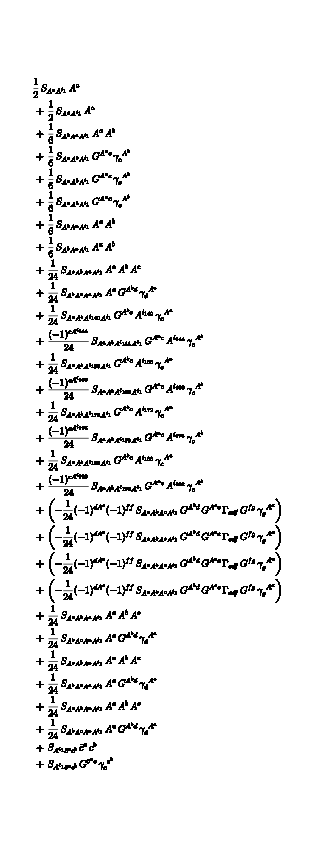

FEx[FTerm[1/2,S[{A,A},{-i439,-i1}],A[i439]],FTerm[1/2,S[{A,A},{-i440,-i1}],A[i440]],FTerm[1/6,S[{A,A,A},{-i442,-i441,-i1}],A[i441],A[i442]],FTerm[1/6,S[{A,A,A},{-i444,-i443,-i1}],Propagator[{A,AnyField},{i444,i445}],γ[{AnyField,A},{-i445,i443}]],FTerm[1/6,S[{A,A,A},{-i447,-i446,-i1}],Propagator[{A,AnyField},{i447,i448}],γ[{AnyField,A},{-i448,i446}]],FTerm[1/6,S[{A,A,A},{-i450,-i449,-i1}],Propagator[{A,AnyField},{i450,i451}],γ[{AnyField,A},{-i451,i449}]],FTerm[1/6,S[{A,A,A},{-i453,-i452,-i1}],A[i452],A[i453]],FTerm[1/6,S[{A,A,A},{-i455,-i454,-i1}],A[i454],A[i455]],FTerm[1/24,S[{A,A,A,A},{-i458,-i457,-i456,-i1}],A[i456],A[i457],A[i458]],FTerm[1/24,S[{A,A,A,A},{-i461,-i460,-i459,-i1}],A[i459],Propagator[{A,AnyField},{i461,i462}],γ[{AnyField,A},{-i462,i460}]],FTerm[1/24,S[{A,A,A,A},{-i464,-i463,-i140,-i1}],Propagator[{A,AnyField},{i463,i465}],A[i140] γ[{AnyField,A},{-i465,i464}]],FTerm[1/24,S[{A,A,A,A},{-i467,-i466,-i144,-i1}],Propagator[{A,AnyField},{i467,i468}],A[i144] FMinus[{AnyField,A},{i468,i144}] γ[{AnyField,A},{-i468,i466}]],FTerm[1/24,S[{A,A,A,A},{-i470,-i469,-i156,-i1}],Propagator[{A,AnyField},{i469,i471}],A[i156] γ[{AnyField,A},{-i471,i470}]],FTerm[1/24,S[{A,A,A,A},{-i473,-i472,-i160,-i1}],Propagator[{A,AnyField},{i473,i474}],A[i160] FMinus[{AnyField,A},{i474,i160}] γ[{AnyField,A},{-i474,i472}]],FTerm[1/24,S[{A,A,A,A},{-i476,-i475,-i172,-i1}],Propagator[{A,AnyField},{i475,i477}],A[i172] γ[{AnyField,A},{-i477,i476}]],FTerm[1/24,S[{A,A,A,A},{-i479,-i478,-i176,-i1}],Propagator[{A,AnyField},{i479,i480}],A[i176] FMinus[{AnyField,A},{i480,i176}] γ[{AnyField,A},{-i480,i478}]],FTerm[1/24,S[{A,A,A,A},{-i482,-i481,-i188,-i1}],Propagator[{A,AnyField},{i481,i483}],A[i188] γ[{AnyField,A},{-i483,i482}]],FTerm[1/24,S[{A,A,A,A},{-i485,-i484,-i192,-i1}],Propagator[{A,AnyField},{i485,i486}],A[i192] FMinus[{AnyField,A},{i486,i192}] γ[{AnyField,A},{-i486,i484}]],FTerm[-1/24,S[{A,A,A,A},{-i489,-i488,-i487,-i1}],Propagator[{A,AnyField},{i488,i490}],FMinus[{AnyField,A},{i490,i487}] FMinus[{AnyField,AnyField},{i492,i492}],Propagator[{A,AnyField},{i487,i491}],GammaN[{AnyField,AnyField,AnyField},{-i491,-i490,-i492}],Propagator[{AnyField,AnyField},{i492,i493}],γ[{AnyField,A},{-i493,i489}]],FTerm[-1/24,S[{A,A,A,A},{-i496,-i495,-i494,-i1}],Propagator[{A,AnyField},{i495,i497}],FMinus[{AnyField,A},{i497,i494}] FMinus[{AnyField,AnyField},{i499,i499}],Propagator[{A,AnyField},{i494,i498}],GammaN[{AnyField,AnyField,AnyField},{-i498,-i497,-i499}],Propagator[{AnyField,AnyField},{i499,i500}],γ[{AnyField,A},{-i500,i496}]],FTerm[-1/24,S[{A,A,A,A},{-i503,-i502,-i501,-i1}],Propagator[{A,AnyField},{i502,i504}],FMinus[{AnyField,A},{i504,i501}] FMinus[{AnyField,AnyField},{i506,i506}],Propagator[{A,AnyField},{i501,i505}],GammaN[{AnyField,AnyField,AnyField},{-i505,-i504,-i506}],Propagator[{AnyField,AnyField},{i506,i507}],γ[{AnyField,A},{-i507,i503}]],FTerm[-1/24,S[{A,A,A,A},{-i510,-i509,-i508,-i1}],Propagator[{A,AnyField},{i509,i511}],FMinus[{AnyField,A},{i511,i508}] FMinus[{AnyField,AnyField},{i513,i513}],Propagator[{A,AnyField},{i508,i512}],GammaN[{AnyField,AnyField,AnyField},{-i512,-i511,-i513}],Propagator[{AnyField,AnyField},{i513,i514}],γ[{AnyField,A},{-i514,i510}]],FTerm[1/24,S[{A,A,A,A},{-i517,-i516,-i515,-i1}],A[i515],A[i516],A[i517]],FTerm[1/24,S[{A,A,A,A},{-i520,-i519,-i518,-i1}],A[i518],Propagator[{A,AnyField},{i520,i521}],γ[{AnyField,A},{-i521,i519}]],FTerm[1/24,S[{A,A,A,A},{-i524,-i523,-i522,-i1}],A[i522],A[i523],A[i524]],FTerm[1/24,S[{A,A,A,A},{-i527,-i526,-i525,-i1}],A[i525],Propagator[{A,AnyField},{i527,i528}],γ[{AnyField,A},{-i528,i526}]],FTerm[1/24,S[{A,A,A,A},{-i531,-i530,-i529,-i1}],A[i529],A[i530],A[i531]],FTerm[1/24,S[{A,A,A,A},{-i534,-i533,-i532,-i1}],A[i532],Propagator[{A,AnyField},{i534,i535}],γ[{AnyField,A},{-i535,i533}]],FTerm[S[{A,cb,c},{-i1,-i536,-i537}],cb[i536],c[i537]],FTerm[S[{A,cb,c},{-i1,-i538,-i539}],Propagator[{cb,AnyField},{i538,i540}],γ[{AnyField,c},{-i540,i539}]]]

```mathematica
dseA = FMakeDSE[A[i1]]//FPrint
```

To obtain the gap equation, we now take another functional derivative of dseA by using the FTakeDerivatives function . We immediately truncate the result, i . e . insert explicit fields and remove all vertices not specified in the truncation list . The result is plotted, the momentum - routed and printed as LATEX.


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

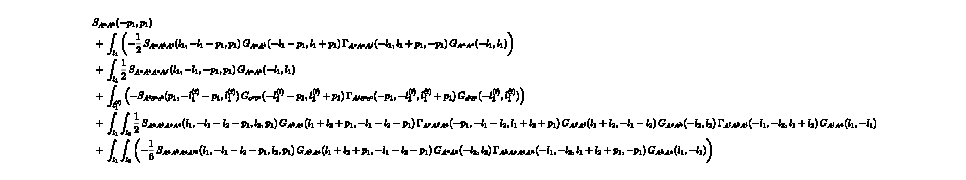

```mathematica
DSEAA=FTakeDerivatives[dseA,{A[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

The momentum routing returns an association, with the result classified according to the number of loops :

```mathematica
DSEAA//Keys
```

{0-Loop,1-Loop,2-Loop}

The corresponding elements of DSEAA contain the "Expression" itself, a list of "ExternalIndices" and the "LoopMomenta" :

```mathematica
DSEAA["1-Loop"]//Keys
```

{Expression,ExternalIndices,LoopMomenta}

```mathematica
Framed@DSEAA["1-Loop"]["Expression"]
Framed@DSEAA["1-Loop"]["ExternalIndices"]
Framed@DSEAA["1-Loop"]["LoopMomenta"]
```

FEx[FTerm[-1/2,S[{A,A,A},{{l1,{v1373,c1374}},{-l1-p1,{v1376,c1377}},{p1,{v1,c1}}}],Propagator[{A,A},{{-l1-p1,{v1379,c1380}},{l1+p1,{v1376,c1377}}}],GammaN[{A,A,A},{{-l1,{v1382,c1383}},{l1+p1,{v1379,c1380}},{-p1,{v2,c2}}}],Propagator[{A,A},{{-l1,{v1373,c1374}},{l1,{v1382,c1383}}}]],FTerm[1/2,S[{A,A,A,A},{{l1,{v1385,c1386}},{-l1,{v1388,c1389}},{-p1,{v2,c2}},{p1,{v1,c1}}}],Propagator[{A,A},{{-l1,{v1385,c1386}},{l1,{v1388,c1389}}}]],FTerm[-1,S[{A,cb,c},{{p1,{v1,c1}},{-lf1-p1,{c1433}},{lf1,{c1435}}}],Propagator[{c,cb},{{-lf1-p1,{c1437}},{lf1+p1,{c1433}}}],GammaN[{A,cb,c},{{-p1,{v2,c2}},{-lf1,{c1439}},{lf1+p1,{c1437}}}],Propagator[{c,cb},{{-lf1,{c1435}},{lf1,{c1439}}}]]]

{i1→{p1,{v1,c1}},i2→{-p1,{v2,c2}}}

{l1|lf1}

Next, we project and trace out only the 1-Loop part of the gluon gap equation. You can do the same to the 2-Loop parts, which takes considerably more time.
We use here the function FMakeDiagrammaticRules to create a list of replacement rules for the tensor bases of all vertices, as specified in the setup.

```mathematica
projectorAA=FTerm[TBGetProjector["AA",1,{i1,i2}/.DSEAA["1-Loop"]["ExternalIndices"]]]
```

FTerm[1/24 deltaAdjCol[c1,c2] transProj[-p1,v1,v2]]

```mathematica
DSEAAProjected=projectorAA**DSEAA["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[];
DSEAAResult=FormTrace[DSEAAProjected]//dressingRules//Simplify//PropParam;
```

The Landau gauge result is obtained by taking ξ=0. We could have also done this beforehand - nevertheless, the 1-loop result reads

```mathematica
DSEAAResult/.ξ->0//Simplify//PropParam
```

{(2 (-1+cospl1^2) gS (3 l1^4+6 cospl1 l1^3 p+(8+cospl1^2) l1^2 p^2+6 cospl1 l1 p^3+3 p^4) ZA3[√(2/3) √(l1^2+cospl1 l1 p+p^2)])/(l1^2 (l1^2+2 cospl1 l1 p+p^2)^2 ZA[l1] ZA[√(l1^2+2 cospl1 l1 p+p^2)]),-((-7+cospl1^2) gS^2)/(l1^2 ZA[l1]),((-1+cospl1^2) gS ZAcbc[√(2/3) √(l1^2+cospl1 l1 p+p^2)])/((l1^2+2 cospl1 l1 p+p^2) Zc[l1] Zc[√(l1^2+2 cospl1 l1 p+p^2)])}

The result can be directly outputted as C++ or Julia code:

```mathematica
MakeCppFunction[Total@DSEAAResult/.ξ->0,"Name"->"DSEAA1Loop","Parameters"->{"l1","p","cospl1","gS","ZA","Zc","ZA3","ZAcbc"}]
MakeJuliaFunction[Total@DSEAAResult/.ξ->0,"Name"->"DSEAA1Loop","Parameters"->{"l1","p","cospl1","gS","ZA","Zc","ZA3","ZAcbc"}]
```

auto DSEAA1Loop(const auto &l1, const auto &p, const auto &cospl1, const auto &gS, const auto &ZA, const auto &Zc,
                const auto &ZA3, const auto &ZAcbc)
{
  const auto _repl1 = ZA(l1);
  const auto _repl2 = powr<2>(l1);
  const auto _repl3 = powr<2>(p);
  const auto _repl4 = powr<2>(cospl1);
  const auto _repl5 = powr<3>(p);
  const auto _repl6 = powr<4>(p);
  const auto _repl7 = powr<-2>(p);
  const auto _repl8 = powr<-4>(l1);
  return (powr<-1>(_repl1)) * ((7.) * ((_repl2) * (_repl3)) + (-1.) * ((_repl2) * ((_repl3) * (_repl4)))) *
             ((_repl7) * ((_repl8) * (powr<2>(gS)))) +
         (-0.5) *
             ((12.) * ((_repl3) * (powr<6>(l1))) +
              (_repl2) *
                  ((-4.) * ((_repl2) * ((_repl3) * (_repl4))) + (-12.) * (_repl6) +
                   (-24.) * ((_repl5) * ((cospl1) * (l1)))) *
                  ((_repl3) * (_repl4)) +
              ((-12.) * ((_repl2) * ((_repl3) * (_repl4))) + (32.) * (_repl6) +
               (24.) * ((_repl5) * ((cospl1) * (l1)))) *
                  (powr<4>(l1)) +
              ((-28.) * ((_repl2) * ((_repl4) * (_repl6))) + (-24.) * ((_repl5) * ((powr<3>(cospl1)) * (powr<3>(l1)))) +
               (24.) * ((cospl1) * ((l1) * (powr<5>(p)))) + (12.) * (powr<6>(p))) *
                  (_repl2)) *
             ((powr<-1>(_repl1)) *
              ((_repl7) *
               ((_repl8) * ((gS) * ((powr<-2>(_repl2 + _repl3 + (2.) * ((cospl1) * ((l1) * (p))))) *
                                    ((powr<-1>(ZA(sqrt(_repl2 + _repl3 + (2.) * ((cospl1) * ((l1) * (p))))))) *
                                     (ZA3((0.5773502691896258) * (sqrt((2.) * (_repl2) + (2.) * (_repl3) +
                                                                       (2.) * ((cospl1) * ((l1) * (p))))))))))))) +
         (gS) * ((-1.) * (_repl2) + (_repl2) * (_repl4)) *
             ((powr<-2>(l1)) *
              ((powr<-1>(_repl2 + _repl3 + (2.) * ((cospl1) * ((l1) * (p))))) *
               ((ZAcbc((0.5773502691896258) *
                       (sqrt((2.) * (_repl2) + (2.) * (_repl3) + (2.) * ((cospl1) * ((l1) * (p))))))) *
                ((powr<-1>(Zc(l1))) * (powr<-1>(Zc(sqrt(_repl2 + _repl3 + (2.) * ((cospl1) * ((l1) * (p)))))))))));
}

function DSEAA1Loop(l1, p, cospl1, gS, ZA, Zc, ZA3, ZAcbc)
  _repl1 = ZA(l1)
  _repl2 = l1^(-4)
  _repl3 = p^(-2)
  _repl4 = l1^2
  _repl5 = p^2
  _repl6 = cospl1^2
  _repl7 = p^3
  _repl8 = p^4
  return (_repl2*_repl3*(7*_repl4*_repl5 - _repl4*_repl5*_repl6)*gS^2)/_repl1 - (_repl2*_repl3*gS*(12*_repl5*l1^6 + _repl4*_repl5*_repl6*(-4*_repl4*_repl5*_repl6 - 12*_repl8 - 24*_repl7*cospl1*l1) + l1^4*(-12*_repl4*_repl5*_repl6 + 32*_repl8 + 24*_repl7*cospl1*l1) + _repl4*(-28*_repl4*_repl6*_repl8 - 24*_repl7*cospl1^3*l1^3 + 24*cospl1*l1*p^5 + 12*p^6))*ZA3(sqrt(2*_repl4 + 2*_repl5 + 2*cospl1*l1*p)/sqrt(3)))/(2*_repl1*(_repl4 + _repl5 + 2*cospl1*l1*p)^2*ZA(sqrt(_repl4 + _repl5 + 2*cospl1*l1*p))) + ((-_repl4 + _repl4*_repl6)*gS*ZAcbc(sqrt(2*_repl4 + 2*_repl5 + 2*cospl1*l1*p)/sqrt(3)))/(l1^2*(_repl4 + _repl5 + 2*cospl1*l1*p)*Zc(l1)*Zc(sqrt(_repl4 + _repl5 + 2*cospl1*l1*p)))
end

The same can be of course done for the ghost propagator:

```mathematica
DSEcbc=FTakeDerivatives[MakeDSE[c[i1]],{cb[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## 3Point

Next, we take a look at the ghost - gluon vertex :

```mathematica
DSEAcbc=FTakeDerivatives[MakeDSE[Setup,c[i1]],{A[i3],cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

This time, we will use a FORM rule to simplify expressions when tracing. For symmetric point projections, FunKit provides methods to make such rules:

```mathematica
Framed@MakeSPFormRule::usage
SP3FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3}]
```

MakeSPFormRule[{l1, l2, ...}, p, {p1, p2, ...}]
Creates a FORM rule for symmetric point momentum configuration.
The first argument is a list of loop momenta {l1, l2, ...}.
The second argument p is the average momentum scale.
The third argument is a list of external leg momenta {p1, p2, ...}.
Projects all momenta to a symmetric configuration with average momentum p.
Crucial for evaluating loop integrals at the symmetric point for RG calculations.

{Vector p1,p2,p3, l1 ,p;
Symbol n;
AutoDeclare CFunction cos;
Set exMom : p1,p2,p3;
Set loopMom : l1;

#define SPOrd "3"

*** project to the SP
#procedure ProjSP()
id FTxsp(p1?exMom,p1?exMom)^-1 = FTxsp(p,p)^-1;
id FTxsp(p1?exMom,p1?exMom) = FTxsp(p,p);
id FTxsp(p1?exMom,p2?exMom)^-1 = (-FTxsp(p,p)/(`SPOrd'-1))^-1;
id FTxsp(p1?exMom,p2?exMom) = -FTxsp(p,p)/(`SPOrd'-1);

id FTxsp(p1?exMom,l1?loopMom)^-1 = (sqrt(FTxsp(p,p))*sqrt(FTxsp(l1,l1))*cos(p1,l1))^-1;
id FTxsp(p1?exMom,l1?loopMom) = (sqrt(FTxsp(p,p))*sqrt(FTxsp(l1,l1))*cos(p1,l1));
#endprocedure

#call SCALL(ProjSP)
.sort}

In the above, SCALL is a predefined routine to recursively apply a method to arguments. Even if you do not understand FORM, you can still use it to project to the symmetric  point when tracing as in the following:

```mathematica
projectorAcbc=FTerm[TBGetProjector["Acbc",1,{i3,i2,i1}/.DSEAcbc["1-Loop"]["ExternalIndices"]]];
DSEAcbcProjected=projectorAcbc**DSEAcbc["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[];
DSEAcbcResult=FormTrace[DSEAcbcProjected,{},SP3FormRule]//dressingRules//SP3Project//SPParam//Simplify;
```

To create C++ code, we would now like to insert some user-defined code to define the angles between the loop momentum l1 and the external momenta p1:

```mathematica
Options["MakeCppFunction"]
```

{Return→auto,Parameters→{},Name→function,Prefix→,Suffix→,CodeParser→Cpp,Body→,Class→,Templates→{}}

```mathematica
MakeCppFunction[Total@DSEAcbcResult,
"Name"->"DSEAcbc1Loop",
"Parameters"->{"l1","p","cos1","cos2","gS","ZA","Zc","ZA3","ZAcbc"},
"Body"->"// This is user-defined 
const double cosl1p1 = cos1;
const double cosl1p2 = ((-1.) * (cos1) + (sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2)) * (0.5);
const double cosl1p3 = ((-1.) * (cos1) + (-1.) * ((sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2))) * (0.5);
// This is not user-defined "
]
```

auto DSEAcbc1Loop(const auto &l1, const auto &p, const auto &cos1, const auto &cos2, const auto &gS, const auto &ZA,
                  const auto &Zc, const auto &ZA3, const auto &ZAcbc)
{
  // This is user-defined
  const double cosl1p1 = cos1;
  const double cosl1p2 = ((-1.) * (cos1) + (sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2)) * (0.5);
  const double cosl1p3 = ((-1.) * (cos1) + (-1.) * ((sqrt(3. + (-3.) * (powr<2>(cos1)))) * (cos2))) * (0.5);
  // This is not user-defined
  const auto _repl1 = Zc(sqrt(powr<2>(l1) + (2.) * ((cosl1p1) * ((l1) * (p))) + powr<2>(p)));
  const auto _repl2 = ZA(l1);
  const auto _repl3 = powr<2>(p);
  const auto _repl4 = powr<2>(l1);
  const auto _repl5 = powr<2>(cosl1p2);
  const auto _repl6 = powr<3>(l1);
  const auto _repl7 = powr<3>(p);
  const auto _repl8 = powr<-2>(l1);
  return (0.5) *
             ((-3.) * (_repl7) + (-2.) * ((_repl6) * (cosl1p2)) + (-5.) * ((_repl3) * ((cosl1p2) * (l1))) +
              (-6.) * ((_repl4) * (p)) + (2.) * ((_repl4) * ((_repl5) * (p))) +
              (2.) * ((2.) * ((cosl1p2) * (l1)) + (7.) * (p)) * ((powr<3>(cosl1p1)) * ((l1) * (p))) +
              (2.) *
                  ((2.) * (_repl6 + (6.) * ((_repl3) * (l1))) * (cosl1p2) + (3.) * (_repl3 + (2.) * (_repl4)) * (p)) *
                  (powr<2>(cosl1p1)) +
              ((2. + (-4.) * (_repl5)) * (_repl6) + (6.) * ((_repl7) * (cosl1p2)) +
               (_repl3) * (-7. + (10.) * (_repl5)) * (l1) +
               (2.) * (5. + (-2.) * (_repl5)) * ((_repl4) * ((cosl1p2) * (p)))) *
                  (cosl1p1)) *
             ((powr<-1>(_repl1)) *
              ((powr<-1>(_repl2)) *
               ((_repl8) *
                ((gS) *
                 ((p) * ((powr<-1>(_repl3 + _repl4 + (2.) * ((cosl1p1) * ((l1) * (p))))) *
                         ((powr<-2>(_repl3 + _repl4 + (2.) * (cosl1p1 + cosl1p2) * ((l1) * (p)))) *
                          ((powr<-1>(ZA(sqrt(_repl3 + _repl4 + (2.) * (cosl1p1 + cosl1p2) * ((l1) * (p)))))) *
                           ((ZA3((0.816496580927726) * (sqrt(_repl3 + _repl4 + (l1) * (cosl1p1 + cosl1p2) * (p))))) *
                            (ZAcbc(sqrt(_repl3 + (0.6666666666666666) * (_repl4) +
                                        (0.6666666666666666) * ((2.) * (cosl1p1) + cosl1p2) * ((l1) * (p)))))))))))))) +
         (-0.25) * (1. + (2.) * ((cosl1p1) * (cosl1p2))) *
             ((powr<-1>(_repl1)) * ((2.) * ((cosl1p1) * (l1)) + (-2.) * ((cosl1p2) * (l1)) + (3.) * (p)) *
              ((powr<-1>(_repl2)) *
               ((_repl8) *
                ((gS) * ((p) * ((powr<-1>(_repl3 + _repl4 + (2.) * ((cosl1p1) * ((l1) * (p))))) *
                                ((powr<-1>(_repl3 + _repl4 + (-2.) * ((cosl1p2) * ((l1) * (p))))) *
                                 ((ZAcbc(sqrt(_repl3 + (0.6666666666666666) * (_repl4) +
                                              (0.6666666666666666) * (cosl1p1 + (-1.) * (cosl1p2)) * ((l1) * (p))))) *
                                  ((ZAcbc((0.816496580927726) *
                                          (sqrt(_repl3 + _repl4 + (-1.) * ((cosl1p2) * ((l1) * (p))))))) *
                                   (powr<-1>(Zc(sqrt(_repl3 + _repl4 + (-2.) * ((cosl1p2) * ((l1) * (p))))))))))))))));
}

Once again, we can also take a look at the three - gluon vertex :

-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

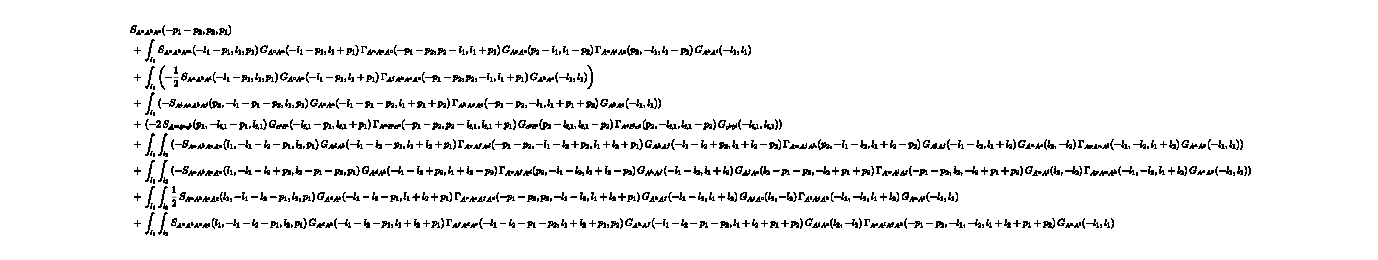

```mathematica
DSEA3=FTakeDerivatives[MakeDSE[Setup,A[i1]],{A[i3],A[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

## 4Point

Or the four - gluon vertex :

```mathematica
DSEA4=FTakeDerivatives[MakeDSE[Setup,A[i1]],{A[i4],A[i3],A[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## fRG

In the following, we list as examples also the fRG flow equations for the Yang-Mills setup we defined.

On a side - note, note that FTakeDerivatives automatically detects symmetries, e . g . for a three - point function:

```mathematica
fRGP3A=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}];
fRGP3A[[-1]]
```

Symmetries→{<|Rule→{},Factor→1|>,<|Rule→{i2→i3,i3→i2},Factor→1|>,<|Rule→{i1→i2,i2→i1},Factor→1|>,<|Rule→{i1→i2,i2→i3,i3→i1},Factor→1|>,<|Rule→{i1→i3,i2→i1,i3→i2},Factor→1|>,<|Rule→{i1→i3,i3→i1},Factor→1|>}

In any FEx[...] you may add as an annotation a rule called “Symmetries”, which explains all possible permutations of external indices which affects the full diagram with a definite Factor (usually either 1 (symmetry) or -1 (antisymmetry)). FTakeDerivatives derives these symmetries always and annotates its result with them. Then, the diagrams are automatically simplified (i.e. identical ones can be identified) and put together, often considerably shortening the resulting expressions.
If you would like to turn off this behaviour, you can use FSetAutoBuildSymmetryList[False]

## 2-Point


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRGAA=FTakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
fRGcbc=FTakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## 3Point

```mathematica
fRGAcbc=FTakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRGA3=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## 4Point

```mathematica
fRGA4=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-